```mathematica
griddir="D:\\Files\\Research\\Thesis\\simgrid.h5";
vars=Import[griddir]
```

{/h2,/alt,/y,/phi,/h3x2i,/e2,/x2,/h2x2i,/glon,/dx1h,/z,/dx3b,/glat,/dx2h,/e1,/x3,/dx2b,/h3x1i,/dx3h,/theta,/gx3,/h2x1i,/h3x3i,/gx2,/h1,/h1x3i,/Bmag,/h1x1i,/x1i,/e3,/h1x2i,/x2i,/etheta,/h2x3i,/h3,/I,/ephi,/er,/gx1,/r,/x,/x1,/nullpts,/x3i,/dx1b}

#### { 1 , 2 , 3 } = { North , East , Up } h# = all ones h#x#i = all ones e# = unit vectors dx#h = differences[x#i] dx#b = differences[x#] gx# = mostly zeroes Bmag = all -0.00005 x#i = x# interpolated? I = all 90 nullpts = all zeros

```mathematica
(*data=Import[griddir,#]&/@vars;
MapThread[{#1,#2}&,{vars,(Dimensions/@data)}]//TableForm*)
```

## Default [m]: { x2 , x3 , x1 }

```mathematica
elem1t=Import[griddir,"/x2"];
elem2t=Import[griddir,"/x3"];
elem3t=Import[griddir,"/x1"];
elem1=Transpose[ConstantArray[elem1t,{Length[elem2t],Length[elem3t]}],{1,3,2}];
elem2=Transpose[ConstantArray[elem2t,{Length[elem1t],Length[elem3t]}],{2,3,1}];
elem3=Transpose[ConstantArray[elem3t,{Length[elem1t],Length[elem2t]}],{2,1,3}];
elem123=Transpose[{elem1,elem2,elem3},{4,1,2,3}];
Dimensions/@{elem1,elem2,elem3}
MinMax@Flatten[elem1]
MinMax@Flatten[elem2]
MinMax@Flatten[elem3]
ListPointPlot3D[{
Join[elem123[[;;,1,1]],elem123[[;;,-1,1]],elem123[[;;,1,-1]],elem123[[;;,-1,-1]]]
,Join[elem123[[1,;;,1]],elem123[[-1,;;,1]],elem123[[1,;;,-1]],elem123[[-1,;;,-1]]]
,Join[elem123[[1,1,;;]],elem123[[-1,1,;;]],elem123[[1,-1,;;]],elem123[[-1,-1,;;]]]
}
,ImageSize->Large
,PlotLegends->{"1","2","3"}
,AxesLabel->{"x2","x3","x1"}
,BoxRatios->((-Subtract@@MinMax@Flatten[#])&/@{elem1,elem2,elem3})
]
```

{{220,148,169},{220,148,169},{220,148,169}}

{-1.72833×10^6,1.72833×10^6}

{-616889.,616889.}

{75882.1,987359.}

-Graphics3D-

## Default Angular [deg/m]: { phi , theta , r }

```mathematica
elem1=Import[griddir,"/phi"];
elem2=Import[griddir,"/theta"];
elem3=Import[griddir,"/r"];
elem123=Transpose[{elem1,elem2,elem3},{4,1,2,3}];
Dimensions/@{elem1,elem2,elem3}
MinMax@Flatten[elem1]
MinMax@Flatten[elem2]
MinMax@Flatten[elem3]
ListPointPlot3D[{
Join[elem123[[;;,1,1]],elem123[[;;,-1,1]],elem123[[;;,1,-1]],elem123[[;;,-1,-1]]]
,Join[elem123[[1,;;,1]],elem123[[-1,;;,1]],elem123[[1,;;,-1]],elem123[[-1,;;,-1]]]
,Join[elem123[[1,1,;;]],elem123[[-1,1,;;]],elem123[[1,-1,;;]],elem123[[-1,-1,;;]]]
}
,ImageSize->Large
,PlotLegends->{"1","2","3"}
,AxesLabel->{"phi","theta","r"}
,BoxRatios->((-Subtract@@MinMax@Flatten[#])&/@{elem1,2elem2,0.5 10^-6 elem3})
]
```

{{216,144,165},{216,144,165},{216,144,165}}

{3.84639,5.03366}

{0.343709,0.524757}

{6.45×10^6,7.32146×10^6}

-Graphics3D-

## Geographical Real [m]: { x , y , z }

```mathematica
elem1=Import[griddir,"/x"];
elem2=Import[griddir,"/y"];
elem3=Import[griddir,"/z"];
elem123=Transpose[{elem1,elem2,elem3},{4,1,2,3}];
Dimensions/@{elem1,elem2,elem3}
MinMax@Flatten[elem1]
MinMax@Flatten[elem2]
MinMax@Flatten[elem3]
ListPointPlot3D[{
Join[elem123[[;;,1,1]],elem123[[;;,-1,1]],elem123[[;;,1,-1]],elem123[[;;,-1,-1]]]
,Join[elem123[[1,;;,1]],elem123[[-1,;;,1]],elem123[[1,;;,-1]],elem123[[-1,;;,-1]]]
,Join[elem123[[1,1,;;]],elem123[[-1,1,;;]],elem123[[1,-1,;;]],elem123[[-1,-1,;;]]]
}
,ImageSize->Large
,PlotLegends->{"1","2","3"}
,AxesLabel->{"x","y","z"}
,BoxRatios->((-Subtract@@MinMax@Flatten[#])&/@{elem1,elem2,elem3})
]
```

{{216,144,165},{216,144,165},{216,144,165}}

{-2.79412×10^6,1.15829×10^6}

{-3.66806×10^6,-1.40819×10^6}

{5.58213×10^6,6.89324×10^6}

-Graphics3D-

## Geographical Angular [deg/m]: { glon , glat , alt }

```mathematica
elem1=Import[griddir,"/glon"];
elem2=Import[griddir,"/glat"];
elem3=Import[griddir,"/alt"];
elem123=Transpose[{elem1,elem2,elem3},{4,1,2,3}];
Dimensions/@{elem1,elem2,elem3}
MinMax@Flatten[elem1]
MinMax@Flatten[elem2]
MinMax@Flatten[elem3]
ListPointPlot3D[{
Join[elem123[[;;,1,1]],elem123[[;;,-1,1]],elem123[[;;,1,-1]],elem123[[;;,-1,-1]]]
,Join[elem123[[1,;;,1]],elem123[[-1,;;,1]],elem123[[1,;;,-1]],elem123[[-1,;;,-1]]]
,Join[elem123[[1,1,;;]],elem123[[-1,1,;;]],elem123[[1,-1,;;]],elem123[[-1,-1,;;]]]
}
,ImageSize->Large
,PlotLegends->{"1","2","3"}
,AxesLabel->{"glon","glat","alt"}
,BoxRatios->((-Subtract@@MinMax@Flatten[#])&/@{elem1,2elem2,3 10^-5 elem3})
]
```

{{216,144,165},{216,144,165},{216,144,165}}

{166.162,240.623}

{55.0206,76.7034}

{80000.,951458.}

-Graphics3D-

```mathematica
elem123[[1,1,-1,;;2]]
elem123[[1,-1,-1,;;2]]
elem123[[-1,1,-1,;;2]]
elem123[[-1,-1,-1,;;2]]
```

{166.162,67.2742}

{232.983,55.0206}

{180.671,76.7034}

{240.623,64.6767}

## Deltas & Other

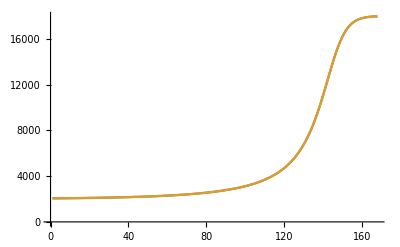

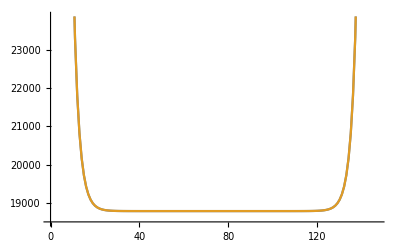

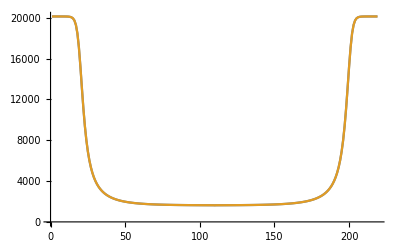

```mathematica
ListLinePlot[{Import[griddir,"/dx1b"],Differences@Import[griddir,"/x1"]}]
ListLinePlot[{Import[griddir,"/dx2b"],Differences@Import[griddir,"/x2"]}]
ListLinePlot[{Import[griddir,"/dx3b"],Differences@Import[griddir,"/x3"]}]
```

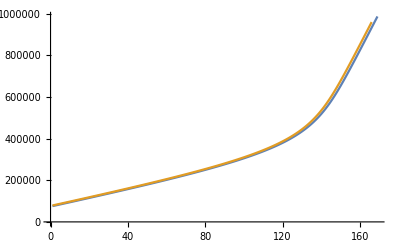

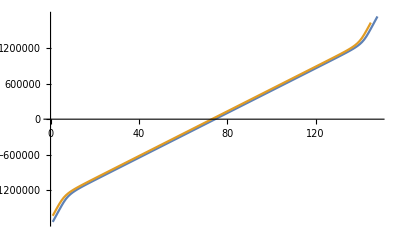

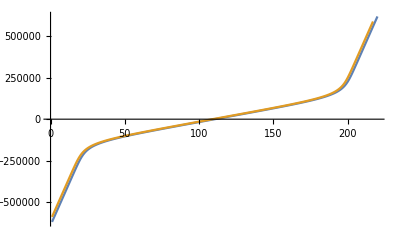

```mathematica
ListLinePlot[{Import[griddir,"/x1"],Import[griddir,"/x1i"]}]
ListLinePlot[{Import[griddir,"/x2"],Import[griddir,"/x2i"]}]
ListLinePlot[{Import[griddir,"/x3"],Import[griddir,"/x3i"]}]
```

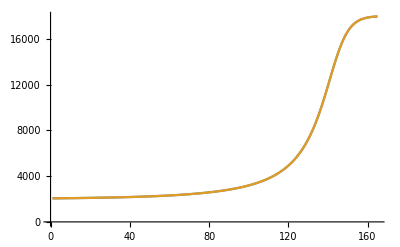

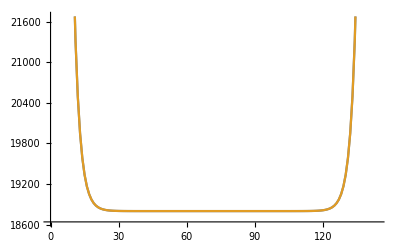

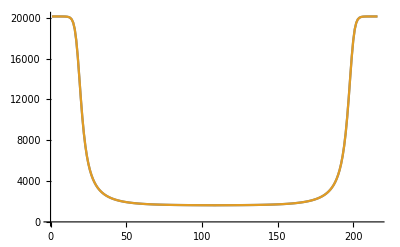

```mathematica
ListLinePlot[{Import[griddir,"/dx1h"],Differences@(Import[griddir,"/x1i"])}]
ListLinePlot[{Import[griddir,"/dx2h"],Differences@(Import[griddir,"/x2i"])}]
ListLinePlot[{Import[griddir,"/dx3h"],Differences@(Import[griddir,"/x3i"])}]
```